```mathematica
xarray=Table[0.5Exp[(Log[10000]-Log[0.5])n/99],{n,0,99}];
carray={1/1000};
barray1=Table[i,{i,0,1,0.01}];
barray2=Table[i,{i,0,20,0.01}];
barray3=Table[0.1Exp[(Log[100]-Log[0.1])n/99],{n,0,99}];
barray4={0,0.01,0.1};
barray6=Table[i,{i,0,20}];
```

```mathematica
(*************************************************************************************************************
```

```mathematica
(*Comparison of the numeric Subscript[X, 0M]^∥(x) and closed formula Subscript[X̃, 0M]^∥(x) for the magnetic forward scattering liongitudinal clouds mesured in units of ξ=(J^2)_⊥√2/πa along the y-axis and in units of 1/a along the horizontal*)
st[ω_,x_]:=Exp[ω](UnitStep[x]+I Gamma[0,ω(I x+1)]/(2Pi))-Exp[-ω]I Gamma[0,ω(I x -1)]/(2Pi)
(*Self-energy: Σ(ω)=(J_⊥/2π)^2 σ(ω).*)
σ[ω_]:=Exp[ω]Gamma[0,ω+10^-10 I]-Exp[-ω]Gamma[0,-ω-10^-10 I]
```

```mathematica
cordc[b_,x_]:= Abs[NIntegrate[Exp[I ω x](st[ω,x]/((ω-b)- σ[ω]/( 1000 Pi))-st[ω,-x]/((ω-b)-  Conjugate[σ[ω]]/(1000Pi)))/(2Pi),{ω,-20,0},Method->"GlobalAdaptive",MaxRecursion->20]]^2
cordcarray=Table[{xarray[[n]],cordc[barray4[[o]],xarray[[n]]]},{o,1,3},{n,1,100}];
```

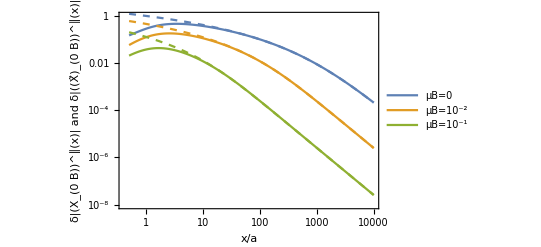

```mathematica
approxmagcor[z_,b_]:=Abs[Exp[z+I b]Gamma[0,z+I b]/(2Pi)]^2;
p1=ListLogLogPlot[cordcarray,Joined->True, BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"x/a","δ|(X_(0  B))^∥(x)| and δ|((X̃)_(0  B))^∥(x)|"},PlotLegends->Placed[{"μB=0","μB=10^-2","μB=10^-1"},{Left,Center}]];
p3=LogLogPlot[{approxmagcor[carray[[1]]x,0 x],approxmagcor[carray[[1]]x,0.01 x],approxmagcor[carray[[1]]x,0.1 x]},{x,.5,10000},PlotStyle->Dashed];
Show[p1,p3]
```

```mathematica
d[b_]:=1/Sqrt[(1/250)^2+b^2]
```

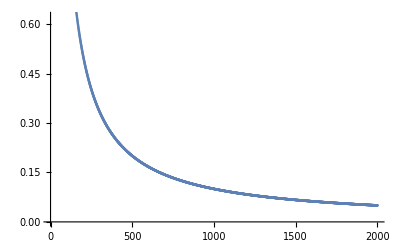

```mathematica
ListPlot[d[barray2]]
```

```mathematica
(*************************************************************************************************************
```

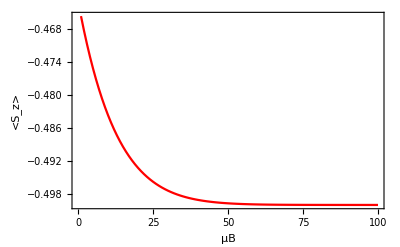

```mathematica
(*Numerical expresion for <d^†d-1/2> in the presence of a magnetic field*)
(*Analytic formula for <d^†d-1/2> in the presance of a magnetic field. Taking the ∑(ω->0) aproximation of the self energy, we get <d^†d-1/2>=-tan^-1(4πμB/(J^2)_⊥)/π *)
corz[b_]:=I NIntegrate[1/((ω-b)- σ[ω]/(75Pi))-1/((ω-b)- Conjugate[σ[ω]]/(75 Pi)),{ω,-20,0},Method->"GlobalAdaptive",MaxRecursion->10]/(2 Pi)-0.5
corzarray=Table[Re[corz[barray3[[o]]]],{o,1,100}];
p2=ListPlot[corzarray,PlotRange->All,Joined->True,PlotStyle->Red,Joined->True, BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"μB","<S_z>"}];
Show[p2]
```

```mathematica
(*************************************************************************************************************
```

```mathematica
(* Numeric calculation of <:(ψ̄)^†(x)ψ̄(x):>
```

```mathematica
(*Subscript[θ, M](x) is defined as*)
stm[ω_,x_]:=(-2Pi I UnitStep[-x]Exp[ω/2]+Exp[ω/2] Gamma[0,ω(1-I x)/2]-Exp[-ω/2] Gamma[0,-ω(I x +1)/2])(-2Pi I UnitStep[x]Exp[ω/2]+Exp[ω/2] Gamma[0,ω(I x+1)/2]-Exp[-ω/2] Gamma[0,ω(I x -1)/2])
```

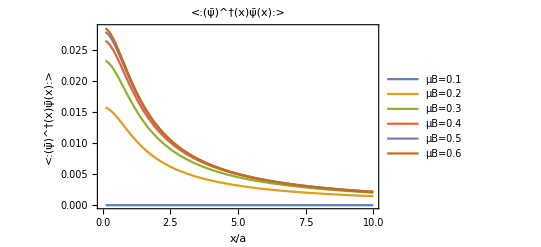

```mathematica
(*Plots of the real and imaginary parts of Subscript[θ, M](x)*)
Plot[{Re[stm[-10^-1,x]],Re[stm[-10^0,x]],Re[stm[-10^1,x]]},{x,-50,50}, BaseStyle->{FontSize->14,FontFamily->"Helvetica"},PlotRange->All,PlotLabel->"Re θ_M(x)",Frame->True,Axes->False,PlotLegends->Placed[{"ω=-0.1","ω=-1","ω=-10"},{Left,Bottom}],FrameLabel->{"x/a","Re θ_M(x)"}];
Plot[{Im[stm[-10^-1,x]],Im[stm[-10^0,x]],Im[stm[-10^1,x]]},{x,-50,50}, BaseStyle->{FontSize->14,FontFamily->"Helvetica"},PlotRange->All,PlotLabel->"Im θ_M(x)",Frame->True,Axes->False,PlotLegends->Placed[{"ω=-0.1","ω=-1","ω=-10"},{Left,Top}],FrameLabel->{"x/a","Im θ_M(x)"}];
(*The magnetic normal ordered expectation value <:(ψ̄)^†(x)ψ̄(x):> is given by*)
corm[b_,x_]:=I(.13)^2 /(4π)NIntegrate[stm[ω,x]/((ω-b)-(.13)^2 σ[ω]/4)-Conjugate[stm[ω,x]]/((ω -b)-(.13)^2 Conjugate[σ[ω]]/4),{ω,-.1,0}]+I(.13)^2 /(4π)NIntegrate[stm[ω,x]/((ω-b)-(.13)^2 σ[ω]/4)-Conjugate[stm[ω,x]]/((ω -b)-(.13)^2 Conjugate[σ[ω]]/4),{ω,-20,-.1}]
barray5=Table[n/10.,{n,0,5}];
xarray2=Table[n/10.,{n,100}];
cormarray=Table[{xarray2[[p]],corm[barray2[[o]],xarray2[[p]]]},{o,1,6},{p,1,100}];
ListPlot[cormarray,Joined->True, BaseStyle->{FontSize->14,FontFamily->"Helvetica"},PlotRange->All,PlotLabel->"<:(ψ̄)^†(x)ψ̄(x):>",Frame->True,Axes->False,FrameLabel->{"x/a","<:(ψ̄)^†(x)ψ̄(x):>"},PlotLegends->Placed[{"μB=0.1","μB=0.2","μB=0.3","μB=0.4","μB=0.5","μB=0.6"},{Right,Top}]]
```

```mathematica
(*************************************************************************************************************
```

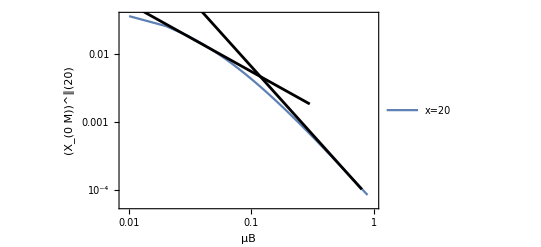

```mathematica
cordc[b_,x_]:= Abs[NIntegrate[Exp[I ω x](st[ω,x]/((ω-b)- σ[ω]/( 75 Pi))-st[ω,-x]/((ω-b)-  Conjugate[σ[ω]]/(75Pi)))/(2Pi),{ω,-20,0},Method->"GlobalAdaptive",MaxRecursion->20]]^2
cordcarray=Table[{barray2[[o]],cordc[barray2[[o]],20]},{o,1,90}];
p1=ListLogLogPlot[cordcarray,Joined->True, BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"μB","(X_(0  M))^∥(20)"},PlotLegends->Placed[{"x=20"},{Left,Bottom}]];
p2=LogLogPlot[0.00055/(b),{ b,0.001,0.3},PlotStyle->{Black,Thickness[0.005]}];
p3=LogLogPlot[0.000065/(b^2),{ b,0.001,0.8},PlotStyle->{Black,Thickness[0.005]}];
Show[p1,p2,p3]
```

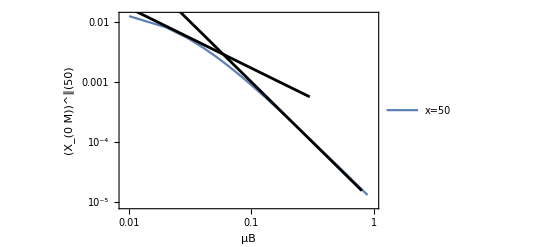

```mathematica
cordc[b_,x_]:= Abs[NIntegrate[Exp[I ω x](st[ω,x]/((ω-b)- σ[ω]/( 75 Pi))-st[ω,-x]/((ω-b)-  Conjugate[σ[ω]]/(75Pi)))/(2Pi),{ω,-20,0},Method->"GlobalAdaptive",MaxRecursion->20]]^2
cordcarray=Table[{barray2[[o]],cordc[barray2[[o]],50]},{o,1,90}];
p1=ListLogLogPlot[cordcarray,Joined->True, BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"μB","(X_(0  M))^∥(50)"},PlotLegends->Placed[{"x=50"},{Left,Bottom}]];
p2=LogLogPlot[0.00017/(b),{ b,0.001,0.3},PlotStyle->{Black,Thickness[0.005]}];
p3=LogLogPlot[0.00001/(b^2),{ b,0.001,0.8},PlotStyle->{Black,Thickness[0.005]}];
Show[p1,p2,p3]
```

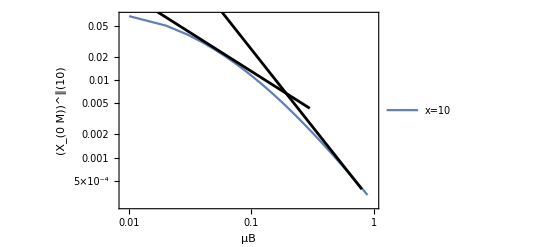

```mathematica
cordc[b_,x_]:= Abs[NIntegrate[Exp[I ω x](st[ω,x]/((ω-b)- σ[ω]/( 75 Pi))-st[ω,-x]/((ω-b)-  Conjugate[σ[ω]]/(75Pi)))/(2Pi),{ω,-20,0},Method->"GlobalAdaptive",MaxRecursion->20]]^2
cordcarray=Table[{barray2[[o]],cordc[barray2[[o]],10]},{o,1,90}];
p1=ListLogLogPlot[cordcarray,Joined->True, BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"μB","(X_(0  M))^∥(10)"},PlotLegends->Placed[{"x=10"},{Left,Bottom}]];
p2=LogLogPlot[0.0013/(b),{ b,0.001,0.3},PlotStyle->{Black,Thickness[0.005]}];
p3=LogLogPlot[0.00025/(b^2),{ b,0.001,0.8},PlotStyle->{Black,Thickness[0.005]}];
Show[p1,p2,p3]
```